```mathematica
(*样本点数*)
Sample=100;
dx=1/(Sample+1);
(*定义离散化后的导数矩阵*)
D1=1/(2  dx)*Table[If[i==j+1,-1,If[i==j-1,1,0]],{i,1,Sample},{j,1,Sample}];
(*另外考虑到u(x)的周期性，需要对导数矩阵周期性处理，体现周期性边界条件*)
(*注意一阶导数的差分定义要首先保证H的厄米性，否则会有不符合物理意义的解(本征值)*)
D1[[1,Sample]]=-1/(2 dx);
D1[[Sample,1]]=1/(2 dx);
(*二阶导的定义完全类似*)
D2=1/(dx)^2*Table[If[i==j,-2,If[i==j-1,1,If[i==j+1,1,0]]],{i,1,Sample},{j,1,Sample}];
D2[[1,Sample]]=1/dx^2;
D2[[Sample,1]]=1/dx^2;
(*定义势能纯函数*)
Potential[x_]:=If[0.25<x && x<0.75,-20,0];
(*定义势能矩阵*)
V=Table[If[i==j,Potential[i dx],0],{i,1,Sample},{j,1,Sample}];
```

```mathematica
(*求本征能量*)
```

```mathematica
Energy[qa_,n_]:=qa^2+Sort[Eigenvalues[N[-D2+2 qa /I*D1 + V]]//Chop][[n]];
Energy[π,1]
(*在矩阵外使用数值计算N[]能大大加快本征值计算速度*)
```

-6.77261

```mathematica
TableForm[Table[Energy[qa,n],{n,1,2},{qa,{-Pi,-Pi/2,0,Pi/2,Pi}}],TableHeadings->{{1,2},{-π,-π/2,0,π/2,π}}]
```

| -π | -π/2 | 0 | π/2 | π
1 | -6.77261 | -10.0067 | -11.9549 | -10.0067 | -6.77264
2 | 5.84137 | 14.1147 | 29.6386 | 14.1147 | 5.84137

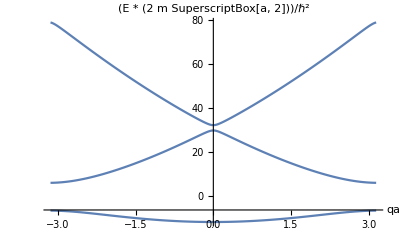

```mathematica
Show[ListPlot[Table[{qa,Energy[qa,1]},{qa,-Pi,Pi,Pi/100}],Joined->True],ListPlot[Table[{qa,Energy[qa,2]},{qa,-Pi,Pi,Pi/100}],Joined->True],ListPlot[Table[{qa,Energy[qa,3]},{qa,-Pi,Pi,Pi/100}],Joined->True],PlotRange->All,AxesLabel->{"qa","(E * (2 m SuperscriptBox[a, 2]))/ℏ^2 "}]
```